```mathematica
<<mf21.m
```

```mathematica
cRaleigh2[α_,β_,ν_]:=Module[{answer,pchhmrA,pchhmrB},
pchhmrA=Pochhammer[α,ν];
pchhmrB=Pochhammer[β,ν];
answer=pchhmrA*pchhmrB/(ν!)^2;
Return[answer]]
```

```mathematica
eRaleigh[α_,β_,ν_]:=Sum[1/(α+p)+1/(β+p)-2/(1+p),{p,0,ν-1}]
```

```mathematica
FstarRaleigh2[α_,β_,u_,terms_]:=
Module[{ν,fsr},
fsr=Sum[cRaleigh2[α,β,ν]*eRaleigh[α,β,ν]*u^ν,{ν,1,terms}];
Return[fsr]]
```

```mathematica
Fraleigh2[α_,β_,u_,terms_]:=Sum[cRaleigh2[α,β,ν]*u^ν,{ν,0,terms}]
```

```mathematica
FstarRaleigh3[n_,m_,x_]:=
Module[{α,β,fsr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fsr2=FstarRaleigh2[α,β,x,n];
fsr2=Series[fsr2,{x,0,n}];
Return[fsr2]]
```

```mathematica
Fraleigh4[n_,m_,x_]:=
Module[{α,β,fr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fr2=Fraleigh2[α,β,x,n];
fr2=Series[fr2,{x,0,n}];
Return[fr2]]
```

```mathematica
exNo3[n_,m_,J_]:=
Module[{a1,a2,a3,a4},
a1=J*Exp[FstarRaleigh3[n,m,J]/Fraleigh4[n,m,J]];
a2=Series[a1,{J,0,n}];
a3=Collect[Normal[a2],J];
a4=Series[a3,{J,0,n}];
Return[a4]]
```

```mathematica
J[n_,m_]:=1/InverseSeries[exNo3[n,m,x],x]
```

```mathematica
jNew[n_,m_]:=
Module[{ns,collect1,cf,collect2},
ns=Normal[J[n,m]]/.x->(2^6*m^3*x);
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,-1];
collect2=Collect[collect1/cf,x];(* this division by cf might spoil interpolation *)
Return[collect2]]
```

```mathematica
argPrincipleCircleContour3[f_,center_,radius_,precision_,accuracy_]:=
Module[{gamma,g,hh,int,number},
gamma[t_]:=center+Exp[t*I]*radius;
g[t_]:=f'[t]/f[t];
hh[t_]:=g[gamma[t]]*gamma'[t];
int=NIntegrate[hh[t],{t,0,2*Pi}, WorkingPrecision->precision,AccuracyGoal->accuracy]/(2*Pi*I);
number=Round[int];
Return[number]]
```

```mathematica
For[m=2,m<5,m++;
Print[jNew[5,m]];
Print[test[5,m]]]
```

744+1/x+196884 x+21493760 x^2+864299970 x^3

744+1/x+196884 x+21493760 x^2+864299970 x^3

1664+1/x+1119232 x+394264576 x^2+81264771072 x^3

1664+1/x+1119232 x+394264576 x^2+81264771072 x^3

3160+1/x+4287700 x+3316992000 x^2+1669770821250 x^3

3160+1/x+4287700 x+3316992000 x^2+1669770821250 x^3

```mathematica
For[m=2,m<5,m++;
jn=jNew[5,m];
Print["m ",m];
Print[jn]]
```

m 3

744+1/x+196884 x+21493760 x^2+864299970 x^3

m 4

1664+1/x+1119232 x+394264576 x^2+81264771072 x^3

m 5

3160+1/x+4287700 x+3316992000 x^2+1669770821250 x^3

```mathematica
stream=OpenWrite["run14sept20no1"];
For[m=2,m<302,m++;
jay=jNew[100,m];
Write[stream,{m,jay}]];
Close[stream]
```

run14sept20no1

```mathematica
notA2Q[z_]:=Module[{tf},
tf=True;
If[Abs[z]==2,tf=False];
Return[tf]]
```

```mathematica
nonzeroQ[z_]:=Module[{tf},
tf=True;
If[z==0,tf=False];
Return[tf]]
```

```mathematica
realQ[z_]:=Module[{tf},
tf=False;
If[Im[z]==0,tf=True];
Return[tf]]
```

```mathematica
imaginaryQ[z_]:=Module[{tf},
tf=False;
If[Re[z]==0,tf=True];
Return[tf]]
```

```mathematica
listRoots2[poly_,x_,precision_]:=Module[{sl,solv,rt,at,roots},
sl=Solve[poly==0,x];
solv=secondmap[firstmap[sl]];
rt=reset[solv];
at=imset[solv];
roots=rt+I*at;
Return[N[roots,precision]]]
```

#### I aborted two runs below because execution slowed drastically; below them, I count the zeros of polynomials with the argument principle.

```mathematica
stream=OpenWrite["run14sept20no1"];
For[m=2,m<302,m++;
jay=jNew[100,m];
Write[stream,{m,jay}]];
Close[stream]
```

=======================================================

zeros of polynomial interpolating x^1

length of data file 300

degree of interpolating polynomial = 6

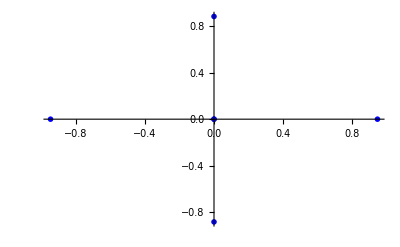

root count,real root count,imaginary root count

{4,2,2}

maximum modulus/d = 0.9455373474749215640964772981974583971286600589341663682184819324310246373247826534080184238479814945

=======================================================

zeros of polynomial interpolating x^2

length of data file 300

degree of interpolating polynomial = 9

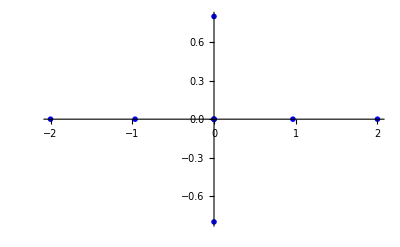

root count,real root count,imaginary root count

{6,4,2}

maximum modulus/d = 0.4827200178513566862197536476910742815034820876310719038729847663428025179821267252897589766126626674

=======================================================

zeros of polynomial interpolating x^3

length of data file 300

degree of interpolating polynomial = 12

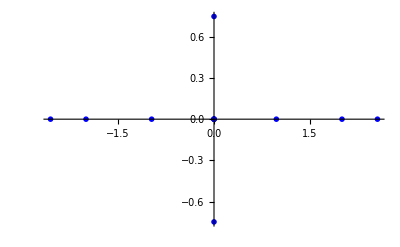

root count,real root count,imaginary root count

{8,6,2}

maximum modulus/d = 0.8514236472326004421750655478050520548260542815159296586685076350419897831166405738239824031357841874

=======================================================

zeros of polynomial interpolating x^4

length of data file 300

degree of interpolating polynomial = 15

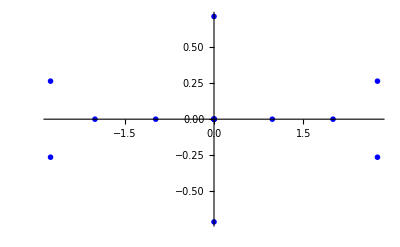

root count,real root count,imaginary root count

{10,4,2}

maximum modulus/d = 0.6897788225265439868302844672408118279425516968280311694544473983876886021149803237038265822064096654

=======================================================

zeros of polynomial interpolating x^5

length of data file 300

degree of interpolating polynomial = 18

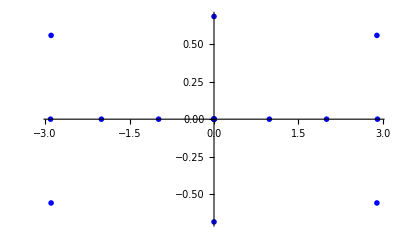

root count,real root count,imaginary root count

{12,6,2}

maximum modulus/d = 0.589410944972086198312785831977171976735908275697314011456308842222850040019510551535216881370825626

=======================================================

zeros of polynomial interpolating x^6

length of data file 300

degree of interpolating polynomial = 21

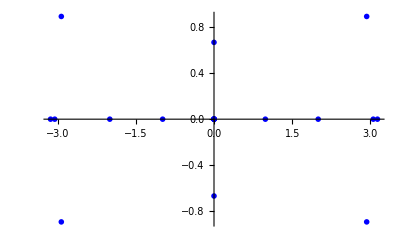

root count,real root count,imaginary root count

{14,8,2}

maximum modulus/d = 0.5228865299209771379571809126941533720556086323920461716369999135309184929906293547567306899693997647

=======================================================

zeros of polynomial interpolating x^7

length of data file 300

degree of interpolating polynomial = 24

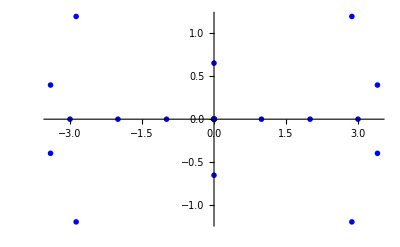

root count,real root count,imaginary root count

{16,6,2}

maximum modulus/d = 0.4893512248647277617819946031492937202982515050736090475325906897725514567283299608041845345418618121

=======================================================

zeros of polynomial interpolating x^8

length of data file 300

degree of interpolating polynomial = 27

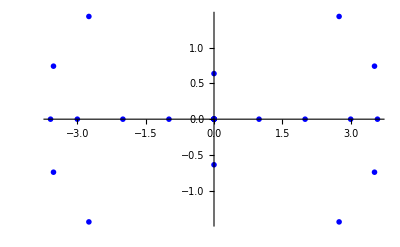

root count,real root count,imaginary root count

{18,8,2}

maximum modulus/d = 0.4500359100078012366099307204927387433932637667739508658980413912330797208824700480587071443519575314

=======================================================

zeros of polynomial interpolating x^9

length of data file 300

degree of interpolating polynomial = 30

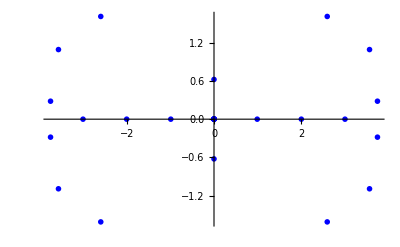

root count,real root count,imaginary root count

{20,6,2}

maximum modulus/d = 0.4171600786341249176485453802737338829820003234498368982272619489506878284207473692843144734840361514

=======================================================

zeros of polynomial interpolating x^10

length of data file 300

degree of interpolating polynomial = 33

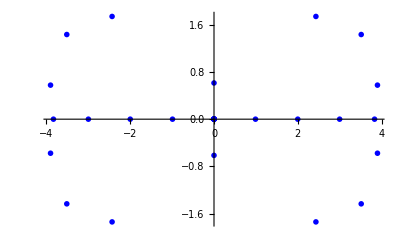

root count,real root count,imaginary root count

{22,8,2}

maximum modulus/d = 0.3945834445167080703407603854826188441714142404391106852175658917145869320617005653106903401993509509

=======================================================

zeros of polynomial interpolating x^11

length of data file 300

degree of interpolating polynomial = 36

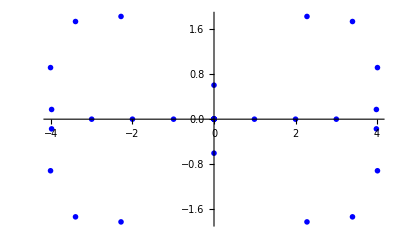

root count,real root count,imaginary root count

{24,6,2}

maximum modulus/d = 0.3738499654739812634670576589984360347686245559718193414661938503781996971151898019524784050927275643

=======================================================

zeros of polynomial interpolating x^12

length of data file 300

degree of interpolating polynomial = 39

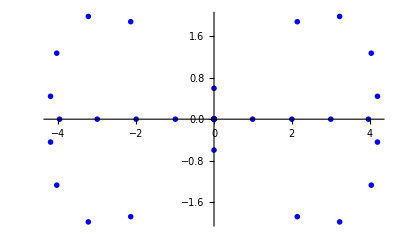

root count,real root count,imaginary root count

{26,8,2}

maximum modulus/d = 0.3529856058115456889628943209647584756508966695494116695777687658940036943249189201669288094049269328

=======================================================

zeros of polynomial interpolating x^13

length of data file 300

degree of interpolating polynomial = 42

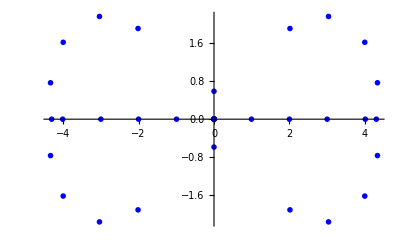

root count,real root count,imaginary root count

{28,10,2}

maximum modulus/d = 0.3385615265961346313383650040745125142493552920274064301865188889085309132804747469438666623225782185

=======================================================

zeros of polynomial interpolating x^14

length of data file 300

degree of interpolating polynomial = 45

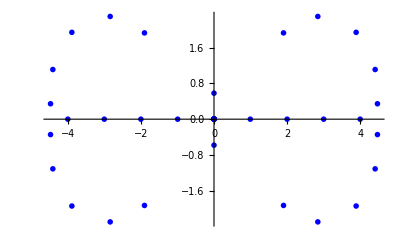

root count,real root count,imaginary root count

{30,8,2}

maximum modulus/d = 0.324662799042278853194363582434076394662650839808638483760097303767189874610313769477863423991713724

=======================================================

zeros of polynomial interpolating x^15

length of data file 300

degree of interpolating polynomial = 48

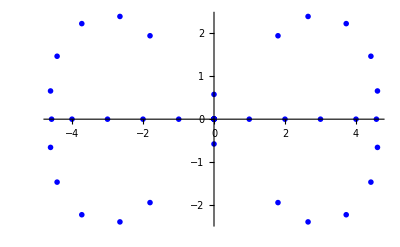

root count,real root count,imaginary root count

{32,10,2}

maximum modulus/d = 0.3103236706073062270738134269879772988937581258433385640070074886827008221394355221995878043678999525

=======================================================

zeros of polynomial interpolating x^16

length of data file 300

degree of interpolating polynomial = 51

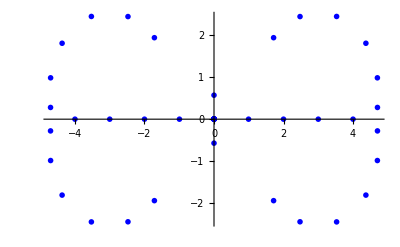

root count,real root count,imaginary root count

{34,8,2}

maximum modulus/d = 0.3001251271242048688836601216772973121177459322685357178129952028627940357098506964641836011554042767

=======================================================

zeros of polynomial interpolating x^17

length of data file 300

degree of interpolating polynomial = 54

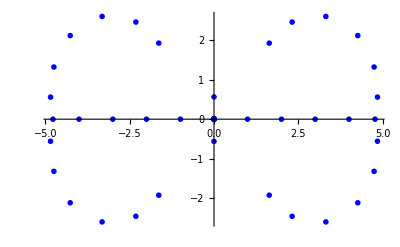

root count,real root count,imaginary root count

{36,10,2}

maximum modulus/d = 0.2897554327518821702699896004442777991379904942581464825566441325301000500117651042907276041800387009

=======================================================

zeros of polynomial interpolating x^18

length of data file 300

degree of interpolating polynomial = 57

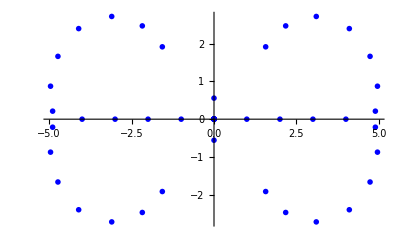

root count,real root count,imaginary root count

{38,8,2}

maximum modulus/d = 0.279678593177308129793711038269668840380209160197282942456137717481666472329180339888235058544498867

=======================================================

zeros of polynomial interpolating x^19

length of data file 300

degree of interpolating polynomial = 60

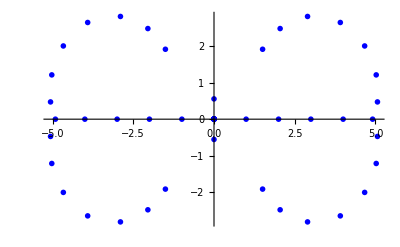

root count,real root count,imaginary root count

{40,10,2}

maximum modulus/d = 0.271983286157065992109247553034403616005150684818846363345854573806691352372626170830357263161031553

=======================================================

zeros of polynomial interpolating x^20

length of data file 300

degree of interpolating polynomial = 63

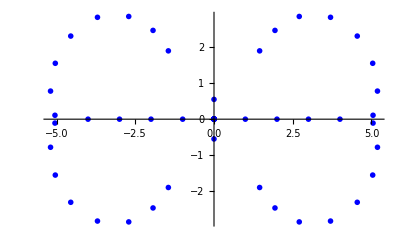

root count,real root count,imaginary root count

{42,8,2}

maximum modulus/d = 0.2636665751101358349107744552502547263781041006864939300554562233251857139888640497942535239452070909

=======================================================

zeros of polynomial interpolating x^21

length of data file 300

degree of interpolating polynomial = 66

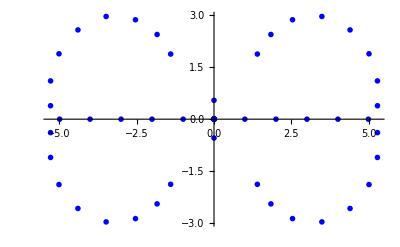

root count,real root count,imaginary root count

{44,10,2}

maximum modulus/d = 0.2566287399791286570544966632334560418233752411057461752322501253094217873646337485856724172086964472

=======================================================

zeros of polynomial interpolating x^22

length of data file 300

degree of interpolating polynomial = 69

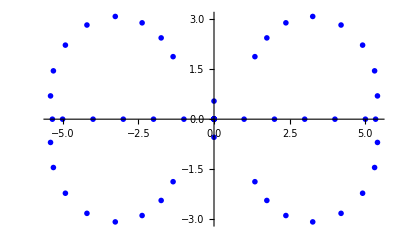

root count,real root count,imaginary root count

{46,12,2}

maximum modulus/d = 0.2502539433568609095462671024851055824435570094751167714788761926238471519847298744537911397672524048

=======================================================

zeros of polynomial interpolating x^23

length of data file 300

degree of interpolating polynomial = 72

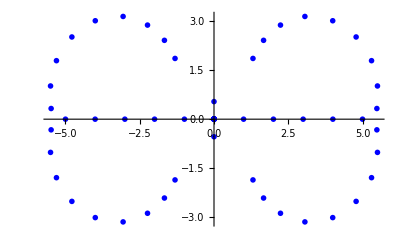

root count,real root count,imaginary root count

{48,10,2}

maximum modulus/d = 0.243277453029606046070419561198120005324422412018929236664582028256754571554150658986451976685620203

=======================================================

zeros of polynomial interpolating x^24

length of data file 300

degree of interpolating polynomial = 75

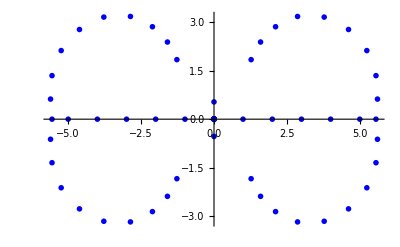

root count,real root count,imaginary root count

{50,12,2}

maximum modulus/d = 0.2382195965675195472330502193074124367422835534557873237691470982928068281323035187768227781551834242

=======================================================

zeros of polynomial interpolating x^25

length of data file 300

degree of interpolating polynomial = 78

$Aborted

**************************************************************

max {roots/d} vs. d

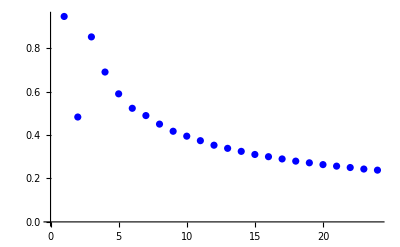

degrees

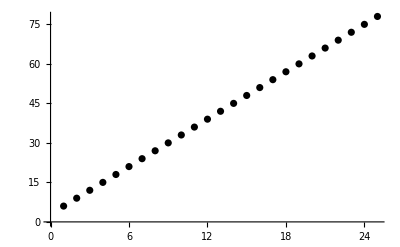

number of impure roots plot

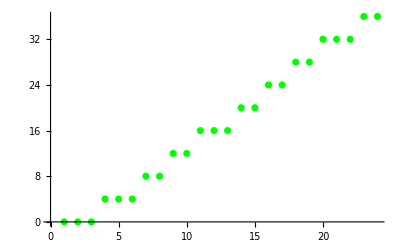

run15sept20no4

```mathematica
rstream=OpenRead["run14sept20no1"];
list=ReadList[rstream];
Close[rstream];
wstream1=OpenWrite["run15sept20no4"];
maxes={};
centers={};
degrees={};
impurenumber={};
precision=100;
truncation=98;
pointsize=.01;
color=Blue;
For[d=0,d<truncation,d++;
data={};
Print["======================================================="];
Print["zeros of polynomial interpolating x^",d];
For[k=0,k<300,k++;
m=list[[k,1]];
srs=list[[k,2]];
srs2=Normal[Series[srs,{x,0,truncation}]];
c=Coefficient[srs2,x,d];
data=Append[data,{m,c}];
] (* k loop *);
Print["length of data file ",Length[data]];
ip=Collect[InterpolatingPolynomial[data,x],x];
degree=Exponent[ip,x];
Print["degree of interpolating polynomial = ",degree];
AppendTo[degrees,{d,degree}];
plotRoots2[ip,x,pointsize,color];
roots=listRoots2[ip,x,precision];
roots=Select[roots,nonzeroQ];
rootsnumber=Length[roots];
realroots=Select[roots,realQ];
realrootsnumber=Length[realroots];
imaginaryroots=Select[roots,imaginaryQ];
imaginaryrootsnumber=Length[imaginaryroots];
Print["root count,real root count,imaginary root count"];
Print[{rootsnumber,realrootsnumber,imaginaryrootsnumber}];
AppendTo[impurenumber,{d,rootsnumber-realrootsnumber-imaginaryrootsnumber}];
pRoots=Select[roots,notA2Q];
max=Max[Abs[pRoots]/d];
Print["maximum modulus/d = ",max];
Write[wstream1,{d,ip,roots,center,max}];
AppendTo[maxes,{d,max}]
];
Print["**************************************************************"];
Print["max {roots/d} vs. d"];
Print[ListPlot[maxes,PlotStyle->Blue]];
Print["degrees"];
Print[ListPlot[degrees,PlotStyle->Black]];
Print["number of impure roots plot"];
Print[ListPlot[impurenumber,PlotStyle->Green]];
Close[wstream1]
```

```mathematica
rstream=OpenRead["run14sept20no1"];
list=ReadList[rstream];
Close[rstream];
Print[Length[list]]
```

300

=======================================================

zeros of polynomial interpolating x^1

length of data file 300

degree of interpolating polynomial = 6

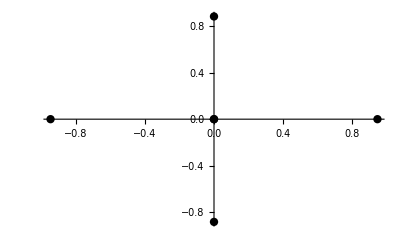

root count,real root count,imaginary root count

{4,2,2}

maximum modulus/d = 0.9455373474749215640964772981974583971286600589341663682184819324310246373247826534080184238479814945

=======================================================

zeros of polynomial interpolating x^2

length of data file 300

degree of interpolating polynomial = 9

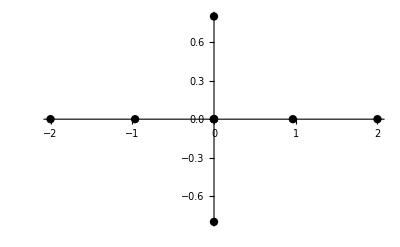

root count,real root count,imaginary root count

{6,4,2}

maximum modulus/d = 0.4827200178513566862197536476910742815034820876310719038729847663428025179821267252897589766126626674

=======================================================

zeros of polynomial interpolating x^3

length of data file 300

degree of interpolating polynomial = 12

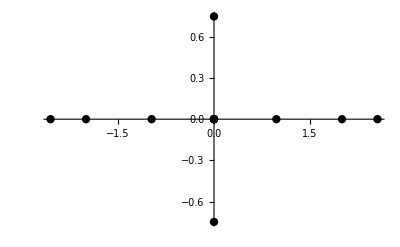

root count,real root count,imaginary root count

{8,6,2}

maximum modulus/d = 0.8514236472326004421750655478050520548260542815159296586685076350419897831166405738239824031357841874

=======================================================

zeros of polynomial interpolating x^4

length of data file 300

degree of interpolating polynomial = 15

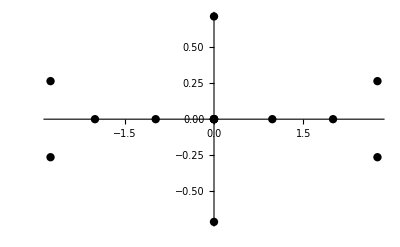

root count,real root count,imaginary root count

{10,4,2}

maximum modulus/d = 0.6897788225265439868302844672408118279425516968280311694544473983876886021149803237038265822064096654

=======================================================

zeros of polynomial interpolating x^5

length of data file 300

degree of interpolating polynomial = 18

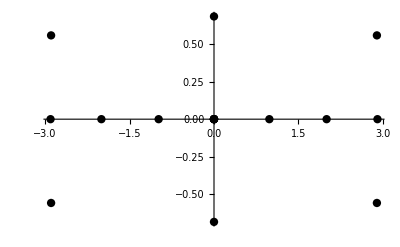

root count,real root count,imaginary root count

{12,6,2}

maximum modulus/d = 0.589410944972086198312785831977171976735908275697314011456308842222850040019510551535216881370825626

=======================================================

zeros of polynomial interpolating x^6

length of data file 300

degree of interpolating polynomial = 21

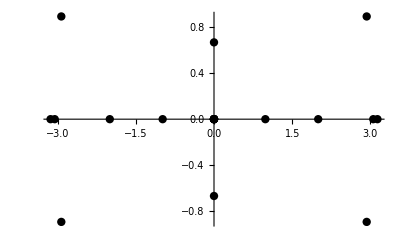

root count,real root count,imaginary root count

{14,8,2}

maximum modulus/d = 0.5228865299209771379571809126941533720556086323920461716369999135309184929906293547567306899693997647

=======================================================

zeros of polynomial interpolating x^7

length of data file 300

degree of interpolating polynomial = 24

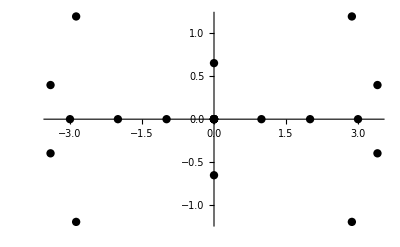

root count,real root count,imaginary root count

{16,6,2}

maximum modulus/d = 0.4893512248647277617819946031492937202982515050736090475325906897725514567283299608041845345418618121

=======================================================

zeros of polynomial interpolating x^8

length of data file 300

degree of interpolating polynomial = 27

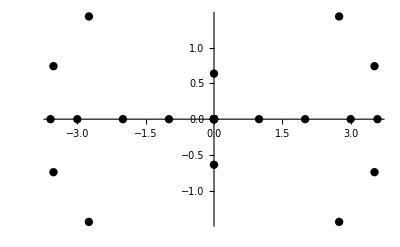

root count,real root count,imaginary root count

{18,8,2}

maximum modulus/d = 0.4500359100078012366099307204927387433932637667739508658980413912330797208824700480587071443519575314

=======================================================

zeros of polynomial interpolating x^9

length of data file 300

degree of interpolating polynomial = 30

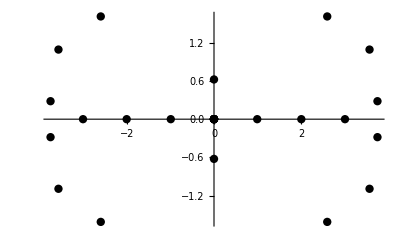

root count,real root count,imaginary root count

{20,6,2}

maximum modulus/d = 0.4171600786341249176485453802737338829820003234498368982272619489506878284207473692843144734840361514

=======================================================

zeros of polynomial interpolating x^10

length of data file 300

degree of interpolating polynomial = 33

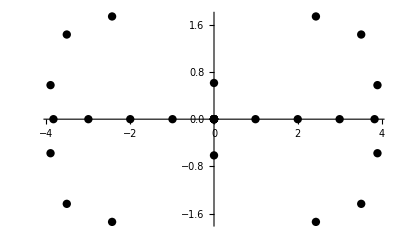

root count,real root count,imaginary root count

{22,8,2}

maximum modulus/d = 0.3945834445167080703407603854826188441714142404391106852175658917145869320617005653106903401993509509

=======================================================

zeros of polynomial interpolating x^11

length of data file 300

degree of interpolating polynomial = 36

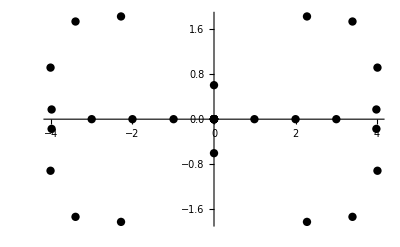

root count,real root count,imaginary root count

{24,6,2}

maximum modulus/d = 0.3738499654739812634670576589984360347686245559718193414661938503781996971151898019524784050927275643

=======================================================

zeros of polynomial interpolating x^12

length of data file 300

degree of interpolating polynomial = 39

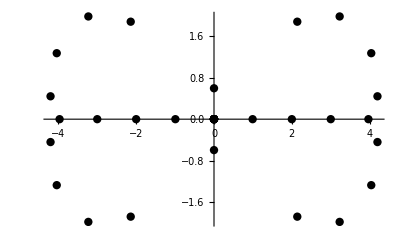

root count,real root count,imaginary root count

{26,8,2}

maximum modulus/d = 0.3529856058115456889628943209647584756508966695494116695777687658940036943249189201669288094049269328

=======================================================

zeros of polynomial interpolating x^13

length of data file 300

degree of interpolating polynomial = 42

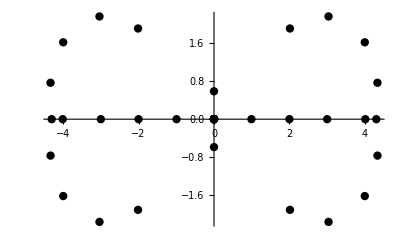

root count,real root count,imaginary root count

{28,10,2}

maximum modulus/d = 0.3385615265961346313383650040745125142493552920274064301865188889085309132804747469438666623225782185

=======================================================

zeros of polynomial interpolating x^14

length of data file 300

degree of interpolating polynomial = 45

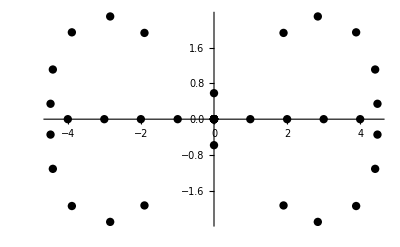

root count,real root count,imaginary root count

{30,8,2}

maximum modulus/d = 0.3246627990422788531943635824340763946626508398086384837600973037671898746103137694778634239917137236

=======================================================

zeros of polynomial interpolating x^15

length of data file 300

degree of interpolating polynomial = 48

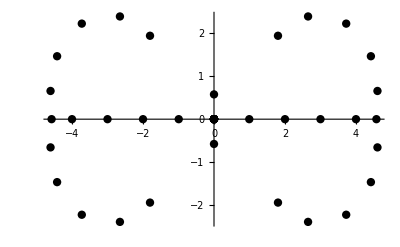

root count,real root count,imaginary root count

{32,10,2}

maximum modulus/d = 0.3103236706073062270738134269879772988937581258433385640070074886827008221394355221995878043678999525

=======================================================

zeros of polynomial interpolating x^16

length of data file 300

degree of interpolating polynomial = 51

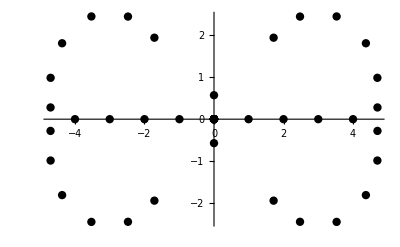

root count,real root count,imaginary root count

{34,8,2}

maximum modulus/d = 0.3001251271242048688836601216772973121177459322685357178129952028627940357098506964641836011554042767

=======================================================

zeros of polynomial interpolating x^17

length of data file 300

degree of interpolating polynomial = 54

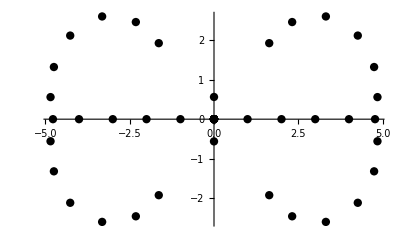

root count,real root count,imaginary root count

{36,10,2}

maximum modulus/d = 0.2897554327518821702699896004442777991379904942581464825566441325301000500117651042907276041800387009

=======================================================

zeros of polynomial interpolating x^18

length of data file 300

degree of interpolating polynomial = 57

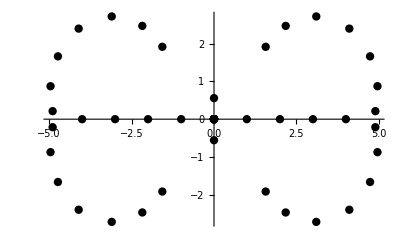

root count,real root count,imaginary root count

{38,8,2}

maximum modulus/d = 0.279678593177308129793711038269668840380209160197282942456137717481666472329180339888235058544498867

=======================================================

zeros of polynomial interpolating x^19

length of data file 300

degree of interpolating polynomial = 60

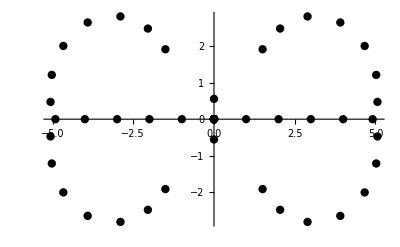

root count,real root count,imaginary root count

{40,10,2}

maximum modulus/d = 0.2719832861570659921092475530344036160051506848188463633458545738066913523726261708303572631610315531

=======================================================

zeros of polynomial interpolating x^20

length of data file 300

degree of interpolating polynomial = 63

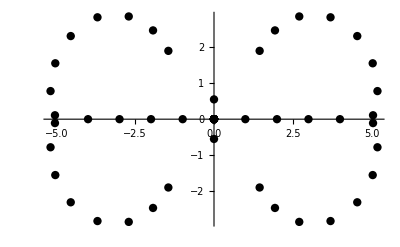

root count,real root count,imaginary root count

{42,8,2}

maximum modulus/d = 0.2636665751101358349107744552502547263781041006864939300554562233251857139888640497942535239452070909

=======================================================

zeros of polynomial interpolating x^21

length of data file 300

degree of interpolating polynomial = 66

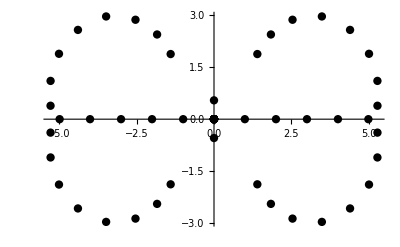

root count,real root count,imaginary root count

{44,10,2}

maximum modulus/d = 0.2566287399791286570544966632334560418233752411057461752322501253094217873646337485856724172086964472

=======================================================

zeros of polynomial interpolating x^22

length of data file 300

degree of interpolating polynomial = 69

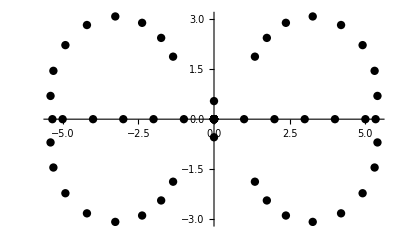

root count,real root count,imaginary root count

{46,12,2}

maximum modulus/d = 0.2502539433568609095462671024851055824435570094751167714788761926238471519847298744537911397672524048

=======================================================

zeros of polynomial interpolating x^23

length of data file 300

degree of interpolating polynomial = 72

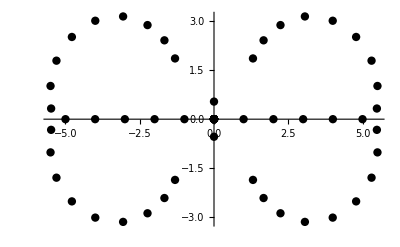

root count,real root count,imaginary root count

{48,10,2}

maximum modulus/d = 0.243277453029606046070419561198120005324422412018929236664582028256754571554150658986451976685620203

=======================================================

zeros of polynomial interpolating x^24

length of data file 300

degree of interpolating polynomial = 75

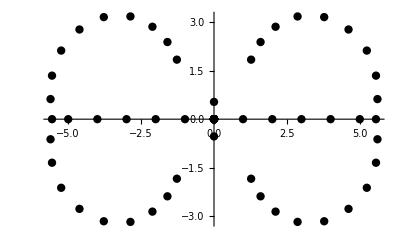

root count,real root count,imaginary root count

{50,12,2}

maximum modulus/d = 0.2382195965675195472330502193074124367422835534557873237691470982928068281323035187768227781551834242

=======================================================

zeros of polynomial interpolating x^25

length of data file 300

degree of interpolating polynomial = 78

$Aborted

**************************************************************

max {roots/d} vs. d

-Graphics-

number of real roots plot

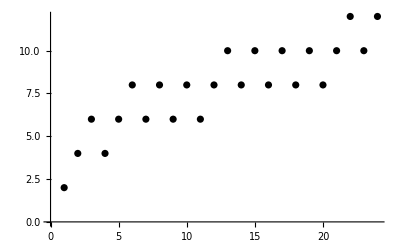

number of real roots data

{{1,2},{2,4},{3,6},{4,4},{5,6},{6,8},{7,6},{8,8},{9,6},{10,8},{11,6},{12,8},{13,10},{14,8},{15,10},{16,8},{17,10},{18,8},{19,10},{20,8},{21,10},{22,12},{23,10},{24,12}}

number of imaginary roots plot

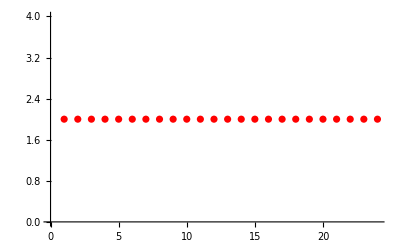

Close::stream: wstream is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close[wstream]

```mathematica
rstream=OpenRead["run14sept20no1"];
list=ReadList[rstream];
Close[rstream];
wstream1=OpenWrite["run29sept20no19"];
pointsize=.015;
color=Black;
maxes={};
centers={};
degrees={};
data={};
realrootsdata={};
imaginaryrootsdata={};
precision=100;
truncation=98;
For[d=0,d<truncation,d++;
data={};
Print["======================================================="];
Print["zeros of polynomial interpolating x^",d];
For[k=0,k<300,k++;
m=list[[k,1]];
srs=list[[k,2]];
srs2=Normal[Series[srs,{x,0,truncation}]];
c=Coefficient[srs2,x,d];
data=Append[data,{m,c}];
] (* k loop *);
Print["length of data file ",Length[data]];
ip=Collect[InterpolatingPolynomial[data,x],x];
degree=Exponent[ip,x];
Print["degree of interpolating polynomial = ",degree];
AppendTo[degrees,{d,degree}];
plotRoots2[ip,x,pointsize,color];
roots=listRoots2[ip,x,precision];
roots=Select[roots,nonzeroQ];
rootsnumber=Length[roots];
realroots=Select[roots,realQ];
realrootsnumber=Length[realroots];
imaginaryroots=Select[roots,imaginaryQ];
imaginaryrootsnumber=Length[imaginaryroots];
Print["root count,real root count,imaginary root count"];
Print[{rootsnumber,realrootsnumber,imaginaryrootsnumber}];
AppendTo[realrootsdata,{d,realrootsnumber}];
AppendTo[imaginaryrootsdata,{d,imaginaryrootsnumber}];
pRoots=Select[roots,notA2Q];
max=Max[Abs[pRoots]/d];
Print["maximum modulus/d = ",max];
Write[wstream1,{d,ip,roots,realrootsnumber,center,max}];
AppendTo[maxes,{d,max}]
];
Print["**************************************************************"];
Print["max {roots/d} vs. d"];
Print[ListPlot[maxes,PlotStyle->Blue]];
Print["number of real roots plot"];
Print[ListPlot[realrootsdata,PlotStyle->Black]];
Print["number of real roots data"];
Print[realrootsdata];
Print["number of imaginary roots plot"];
Print[ListPlot[imaginaryrootsdata,PlotStyle->Red]];
Close[wstream]
```

```mathematica
Print[Map[second,realrootsdata]]
```

{2,4,6,4,6,8,6,8,6,8,6,8,10,8,10,8,10,8,10,8,10,12,10}

#### Compare with earlier calculations (see ‘conjecture 1.nb’)

```mathematica
pstream=OpenRead["run30jun20no19"];
plist=ReadList[pstream];
Close[pstream];
plength=Length[plist];
checkstream=OpenRead["run16jul20no7"];
checklist=ReadList[checkstream];
Close[checkstream];
clength=Length[checklist];
For[k=0,k<3,k++;
Print["-------------------------------------"];
pindex=plist[[k+2,1]];
poly=plist[[k+2,2]];
poly=Collect[poly,x];
Print[{pindex,poly}];
Print[{checklist[[k,1]],checklist[[k,2]]}]]
```

-------------------------------------

{1,-192 x^2-32 x^4+276 x^6}

{1,-192 x^2-32 x^4+276 x^6}

-------------------------------------

{2,(131072 x^3)/27+(32768 x^5)/27-(237568 x^7)/27+2048 x^9}

{2,(131072 x^3)/27+(32768 x^5)/27-(237568 x^7)/27+2048 x^9}

-------------------------------------

{3,-155136 x^4-51712 x^6+332480 x^8-122272 x^10+11202 x^12}

{3,-155136 x^4-51712 x^6+332480 x^8-122272 x^10+11202 x^12}

```mathematica
pstream=OpenRead["run30jun20no19"];
plist=ReadList[pstream];
Close[pstream];
plength=Length[plist];
checkstream=OpenRead["run16jul20no7"];
checklist=ReadList[checkstream];
Close[checkstream];
clength=Length[checklist];
errors={};
For[k=0,k<Min[plength-2,clength],k++;
pindex=plist[[k+2,1]];
poly=plist[[k+2,2]];
poly=Collect[poly,x];
error=poly-checklist[[k,2]];
AppendTo[errors,error]];
Print[errors]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
argPrincipleCircleContour[f_,center_,radius_]:=
Module[{gamma,g,hh,int,number},
gamma[t_]:=center+Exp[t*I]*radius;
g[t_]:=f'[t]/f[t];
hh[t_]:=g[gamma[t]]*gamma'[t];
int=NIntegrate[hh[t],{t,0,2*Pi}, AccuracyGoal->1]/(2*Pi*I);
number=Round[int];
Return[number]]
```

#### In the next two runs, is the routine missing the multiple zeros? No:

```mathematica
For[n=0,n<5,n++;
f[z_]:=(x-1)^n/.x->z;
center=0;
radius=2;
ag=argPrincipleCircleContour[f,center,radius];
Print[{n,ag}]]
```

{1,1}

{2,2}

{3,3}

{4,4}

{5,5}

#### In the language of the paper, d> 2 => the total degree in x of r_d(x) = 3d +3, so a correct interpolation of r_d requires 3d+ 3 pairs (m,c) (in the routines’ notation.) On the other hand, degree of p_d = 2d, so only 2d pairs will generate the correct polynomial. I was generating 300 pairs for each d, so for p_d I was safe keeping d <= 150 and for r_d, keeping d <=31.

#### The runs in question. Exactly half of the zeros fall outside the test disk for d > = 57. What’s special about 57?

```mathematica
rstream=OpenRead["run14sept20no1"];
list=ReadList[rstream];
Close[rstream];
degrees={};
stream=OpenWrite["run17sept20test6"];
center=0;
precision=100;
truncation=98;
pointsize=.01;
color=Blue;
For[d=0,d<truncation,d++;
data={};
For[k=0,k<300,k++;
m=list[[k,1]];
srs=list[[k,2]];
srs2=Normal[Series[srs,{x,0,truncation}]];
c=Coefficient[srs2,x,d];
data=Append[data,{m,c}];
] (* k loop *);
ldf=Length[data];
ip=Collect[InterpolatingPolynomial[data,x],x];
degree=Exponent[ip,x];
AppendTo[degrees,{d,degree}];
radius=d;
f[z_]:=ip/.x->z;
ag=argPrincipleCircleContour[f,center,radius];
If[ag=!=degree,
Print["d: ",d," degree: ",degree," zeros in test disk: ",ag]
];
Write[stream,{d,ip}]
];
Close[stream]
```

d: 2 degree: 9 zeros in test disk: 8

d: 57 degree: 174 zeros in test disk: 87

d: 58 degree: 177 zeros in test disk: 89

d: 59 degree: 180 zeros in test disk: 90

d: 60 degree: 183 zeros in test disk: 92

d: 61 degree: 186 zeros in test disk: 93

d: 62 degree: 189 zeros in test disk: 95

d: 63 degree: 192 zeros in test disk: 96

d: 64 degree: 195 zeros in test disk: 98

d: 65 degree: 198 zeros in test disk: 99

d: 66 degree: 201 zeros in test disk: 101

d: 67 degree: 204 zeros in test disk: 102

d: 68 degree: 207 zeros in test disk: 104

d: 69 degree: 210 zeros in test disk: 105

d: 70 degree: 213 zeros in test disk: 107

d: 71 degree: 216 zeros in test disk: 108

d: 72 degree: 219 zeros in test disk: 110

d: 73 degree: 222 zeros in test disk: 111

d: 74 degree: 225 zeros in test disk: 113

d: 75 degree: 228 zeros in test disk: 114

d: 76 degree: 231 zeros in test disk: 116

d: 77 degree: 234 zeros in test disk: 117

d: 78 degree: 237 zeros in test disk: 119

d: 79 degree: 240 zeros in test disk: 120

d: 80 degree: 243 zeros in test disk: 122

d: 81 degree: 246 zeros in test disk: 123

d: 82 degree: 249 zeros in test disk: 125

d: 83 degree: 252 zeros in test disk: 126

d: 84 degree: 255 zeros in test disk: 128

d: 85 degree: 258 zeros in test disk: 129

d: 86 degree: 261 zeros in test disk: 131

d: 87 degree: 264 zeros in test disk: 132

d: 88 degree: 267 zeros in test disk: 134

d: 89 degree: 270 zeros in test disk: 135

d: 90 degree: 273 zeros in test disk: 137

d: 91 degree: 276 zeros in test disk: 138

d: 92 degree: 279 zeros in test disk: 139

d: 93 degree: 282 zeros in test disk: 141

d: 94 degree: 285 zeros in test disk: 143

d: 95 degree: 288 zeros in test disk: 144

d: 96 degree: 291 zeros in test disk: 146

d: 97 degree: 294 zeros in test disk: 147

d: 98 degree: 297 zeros in test disk: 149

run17sept20test6

```mathematica
rstream=OpenRead["run14sept20no1"];
list=ReadList[rstream];
Close[rstream];
degrees={};
stream=OpenWrite["run20sept20no20"];
center=0;
precision=100;
truncation=98;
pointsize=.01;
color=Blue;
For[d=0,d<truncation,d++;
data={};
For[k=0,k<300,k++;
m=list[[k,1]];
srs=list[[k,2]];
c=Coefficient[srs,x,d];
data=Append[data,{m,c}];
] (* k loop *);
ldf=Length[data];
ip=Collect[InterpolatingPolynomial[data,x],x];
degree=Exponent[ip,x];
AppendTo[degrees,{d,degree}];
radius=d;
f[z_]:=ip/.x->z;
ag=argPrincipleCircleContour[f,center,radius];
If[ag=!=degree,
Print["d: ",d," degree: ",degree," zeros in test disk: ",ag]
];
Write[stream,{d,ip}]
];
Close[stream]
```

d: 2 degree: 9 zeros in test disk: 8

d: 57 degree: 174 zeros in test disk: 87

d: 58 degree: 177 zeros in test disk: 89

d: 59 degree: 180 zeros in test disk: 90

d: 60 degree: 183 zeros in test disk: 92

d: 61 degree: 186 zeros in test disk: 93

d: 62 degree: 189 zeros in test disk: 95

d: 63 degree: 192 zeros in test disk: 96

d: 64 degree: 195 zeros in test disk: 98

d: 65 degree: 198 zeros in test disk: 99

d: 66 degree: 201 zeros in test disk: 101

d: 67 degree: 204 zeros in test disk: 102

d: 68 degree: 207 zeros in test disk: 104

d: 69 degree: 210 zeros in test disk: 105

d: 70 degree: 213 zeros in test disk: 107

d: 71 degree: 216 zeros in test disk: 108

d: 72 degree: 219 zeros in test disk: 110

d: 73 degree: 222 zeros in test disk: 111

d: 74 degree: 225 zeros in test disk: 113

d: 75 degree: 228 zeros in test disk: 114

d: 76 degree: 231 zeros in test disk: 116

d: 77 degree: 234 zeros in test disk: 117

d: 78 degree: 237 zeros in test disk: 119

d: 79 degree: 240 zeros in test disk: 120

d: 80 degree: 243 zeros in test disk: 122

d: 81 degree: 246 zeros in test disk: 123

d: 82 degree: 249 zeros in test disk: 125

d: 83 degree: 252 zeros in test disk: 126

d: 84 degree: 255 zeros in test disk: 128

d: 85 degree: 258 zeros in test disk: 129

d: 86 degree: 261 zeros in test disk: 131

d: 87 degree: 264 zeros in test disk: 132

d: 88 degree: 267 zeros in test disk: 134

d: 89 degree: 270 zeros in test disk: 135

d: 90 degree: 273 zeros in test disk: 137

d: 91 degree: 276 zeros in test disk: 138

d: 92 degree: 279 zeros in test disk: 139

d: 93 degree: 282 zeros in test disk: 141

d: 94 degree: 285 zeros in test disk: 143

d: 95 degree: 288 zeros in test disk: 144

d: 96 degree: 291 zeros in test disk: 146

d: 97 degree: 294 zeros in test disk: 147

d: 98 degree: 297 zeros in test disk: 149

run20sept20no20

```mathematica
stream1=OpenRead["run15sept20no4"];
list1=ReadList[stream1];
Close[stream1];
stream2=OpenRead["run17sept20test6"];
list2=ReadList[stream2];
Close[stream2];
a=Length[list1];
b=Length[list2];
Print[{a,b}]
```

{24,98}

```mathematica
stream1=OpenRead["run15sept20no4"];
list1=ReadList[stream1];
Close[stream1];
stream2=OpenRead["run17sept20test6"];
list2=ReadList[stream2];
Close[stream2];
Print["minimum length: ",Min[Length[list1],Length[list2]]];
no1={};
no2={};
no3={};
For[d=0,d<24,d++;
poly1=list1[[d,2]];
poly2=list2[[d,2]];
If[list1[[d,1]]=!=list2[[d,1]],AppendTo[no1,d]];
If[list1[[d,1]]=!=d,AppendTo[no2,d]];
If[poly1-poly2=!=0,AppendTo[no3,d]]];
Print[no1];
Print[no2];
Print[no3]
```

minimum length: 24

{}

{}

{}

```mathematica
stream1=OpenRead["run17sept20test6"];
list=ReadList[stream1];
Close[stream1];
no1={};
no2={};
For[k=0,k<98,k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
denominator=(x-2)*(x+2)*x^(n+1);
ppoly=poly/denominator;
degree=Exponent[ppoly,x];
ppoly=Series[ppoly,{x,0,degree}];
pp=Collect[ppoly,x];
If[PolynomialQ[pp,x]===False,AppendTo[no1,{n,pp}]];
If[degree=!=2*n,AppendTo[no2,{n,pp}]]];
Print["no1 ",no1];
Print["no2 ",no2]
```

no1 {}

no2 {}

```mathematica
stream1=OpenRead["run17sept20test6"];
list=ReadList[stream1];
Close[stream1];
no1={};
no2={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
denominator=(x-2)*(x+2)*x^(n+1);
ppoly=poly/denominator;
degree=Exponent[ppoly,x];
ppoly=Series[ppoly,{x,0,degree}];
pp=Collect[ppoly,x];
If[PolynomialQ[pp,x]===False,AppendTo[no1,{n,pp}]];
If[degree=!=2*n,AppendTo[no2,{n,pp}]]];
Print["no1 ",no1];
Print["no2 ",no2]
```

no1 {}

no2 {}

```mathematica
stream1=OpenRead["run17sept20test6"];
list=ReadList[stream1];
Close[stream1];
no1={};
no2={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
denominator=(x-2)*(x+2)*x^(n+1);
ppoly=poly/denominator;
degree=Exponent[ppoly,x];
ppoly=Series[ppoly,{x,0,degree}];
pp=Collect[ppoly,x];
If[IrreduciblePolynomialQ[pp]===False,AppendTo[no1,{n,pp}]];
If[degree=!=2*n,AppendTo[no2,{n,pp}]]];
Print["no1 ",no1];
Print["no2 ",no2]
```

no1 {}

no2 {}

```mathematica
no=0;
stream=OpenRead["run17sept20test6"];
list=ReadList[stream];
Close[stream];
center=0;
precision=100;
truncation=98;
pointsize=.01;
color=Blue;
For[k=1,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
denominator=(x-2)*(x+2)*x^(n+1);
ppoly=poly/denominator;
degree=Exponent[ppoly,x];
f[z_]:=ppoly/.x->z;
radius=n;
ag=argPrincipleCircleContour[f,center,radius];
If[ag=!=degree,
no++;
Print["n: ",n," degree: ",degree," zeros in test disk: ",ag]
]
];
Print["no: ",no]
```

NIntegrate::levmaxord: «1» is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating «1» as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

no: 0

```mathematica
no=0;
stream=OpenRead["run17sept20test6"];
list=ReadList[stream];
Close[stream];
center=0;
precision=100;
truncation=98;
pointsize=.01;
color=Blue;
data={};
For[k=1,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
denominator=(x-2)*(x+2)*x^(n+1);
ppoly=poly/denominator;
degree=Exponent[ppoly,x];
f[z_]:=ppoly/.x->z;
radius=N[n/Log[n]];
ag=argPrincipleCircleContour[f,center,radius];
AppendTo[data,{n,degree,ag}];
If[ag=!=degree,
no++;
Print["n: ",n," degree: ",degree," zeros in test disk: ",ag]
]
];
Print["no: ",no];
Print[data]
```

NIntegrate::levmaxord: -4.46954×10^137 ⅇ^(49 ⅈ t)-3.07024×10^140 ⅇ^(51 ⅈ t)+1.39441×10^142 ⅇ^(53 ⅈ t)+4.77651×10^144 ⅇ^(55 ⅈ t)+«65»+3.02434×10^184 ⅇ^(145 ⅈ t)-1.58192×10^184 ⅇ^(147 ⅈ t)+«1» is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating -4.46954×10^137 ⅇ^(49 ⅈ t)-3.07024×10^140 ⅇ^(51 ⅈ t)+1.39441×10^142 ⅇ^(53 ⅈ t)+4.77651×10^144 ⅇ^(55 ⅈ t)+«65»+3.02434×10^184 ⅇ^(145 ⅈ t)-1.58192×10^184 ⅇ^(147 ⅈ t)+«1» as a non-Levin function.

NIntegrate::levmaxord: -1.12548×10^137 ⅇ^(50 ⅈ t)-7.43382×10^139 ⅇ^(52 ⅈ t)+3.25117×10^141 ⅇ^(54 ⅈ t)+1.07391×10^144 ⅇ^(56 ⅈ t)+«65»+2.60808×10^183 ⅇ^(146 ⅈ t)-1.34575×10^183 ⅇ^(148 ⅈ t)+«1» is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating -1.12548×10^137 ⅇ^(50 ⅈ t)-7.43382×10^139 ⅇ^(52 ⅈ t)+3.25117×10^141 ⅇ^(54 ⅈ t)+1.07391×10^144 ⅇ^(56 ⅈ t)+«65»+2.60808×10^183 ⅇ^(146 ⅈ t)-1.34575×10^183 ⅇ^(148 ⅈ t)+«1» as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

no: 0

{{2,4,4},{3,6,6},{4,8,8},{5,10,10},{6,12,12},{7,14,14},{8,16,16},{9,18,18},{10,20,20},{11,22,22},{12,24,24},{13,26,26},{14,28,28},{15,30,30},{16,32,32},{17,34,34},{18,36,36},{19,38,38},{20,40,40},{21,42,42},{22,44,44},{23,46,46},{24,48,48},{25,50,50},{26,52,52},{27,54,54},{28,56,56},{29,58,58},{30,60,60},{31,62,62},{32,64,64},{33,66,66},{34,68,68},{35,70,70},{36,72,72},{37,74,74},{38,76,76},{39,78,78},{40,80,80},{41,82,82},{42,84,84},{43,86,86},{44,88,88},{45,90,90},{46,92,92},{47,94,94},{48,96,96},{49,98,98},{50,100,100},{51,102,102},{52,104,104},{53,106,106},{54,108,108},{55,110,110},{56,112,112},{57,114,114},{58,116,116},{59,118,118},{60,120,120},{61,122,122},{62,124,124},{63,126,126},{64,128,128},{65,130,130},{66,132,132},{67,134,134},{68,136,136},{69,138,138},{70,140,140},{71,142,142},{72,144,144},{73,146,146},{74,148,148},{75,150,150},{76,152,152},{77,154,154},{78,156,156},{79,158,158},{80,160,160},{81,162,162},{82,164,164},{83,166,166},{84,168,168},{85,170,170},{86,172,172},{87,174,174},{88,176,176},{89,178,178},{90,180,180},{91,182,182},{92,184,184},{93,186,186},{94,188,188},{95,190,190},{96,192,192},{97,194,194},{98,196,196}}

```mathematica
no=0;
stream=OpenRead["run17sept20test6"];
list=ReadList[stream];
Close[stream];
center=0;
precision=100;
truncation=98;
pointsize=.01;
color=Blue;
data={};
For[k=1,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
denominator=(x-2)*(x+2)*x^(n+1);
ppoly=poly/denominator;
degree=Exponent[ppoly,x];
f[z_]:=ppoly/.x->z;
radius=N[n/Log[n]^2];
ag=argPrincipleCircleContour[f,center,radius];
AppendTo[data,{n,degree,ag}];
If[ag=!=degree,
no++;
Print["n: ",n," degree: ",degree," zeros in test disk: ",ag]
]
];
Print["no: ",no];
Print[data]
```

n: 3 degree: 6 zeros in test disk: 4

n: 4 degree: 8 zeros in test disk: 4

n: 5 degree: 10 zeros in test disk: 4

n: 6 degree: 12 zeros in test disk: 4

n: 7 degree: 14 zeros in test disk: 4

n: 8 degree: 16 zeros in test disk: 4

n: 9 degree: 18 zeros in test disk: 4

n: 10 degree: 20 zeros in test disk: 4

n: 11 degree: 22 zeros in test disk: 4

n: 12 degree: 24 zeros in test disk: 4

n: 13 degree: 26 zeros in test disk: 4

n: 14 degree: 28 zeros in test disk: 4

n: 15 degree: 30 zeros in test disk: 4

n: 16 degree: 32 zeros in test disk: 4

n: 17 degree: 34 zeros in test disk: 4

n: 18 degree: 36 zeros in test disk: 4

n: 19 degree: 38 zeros in test disk: 4

n: 20 degree: 40 zeros in test disk: 4

n: 21 degree: 42 zeros in test disk: 4

n: 22 degree: 44 zeros in test disk: 6

n: 23 degree: 46 zeros in test disk: 8

n: 24 degree: 48 zeros in test disk: 8

n: 25 degree: 50 zeros in test disk: 8

n: 26 degree: 52 zeros in test disk: 8

n: 27 degree: 54 zeros in test disk: 8

n: 28 degree: 56 zeros in test disk: 8

n: 29 degree: 58 zeros in test disk: 4

n: 30 degree: 60 zeros in test disk: 7

n: 31 degree: 62 zeros in test disk: 12

n: 32 degree: 64 zeros in test disk: 12

n: 33 degree: 66 zeros in test disk: 12

n: 34 degree: 68 zeros in test disk: 12

n: 35 degree: 70 zeros in test disk: 12

n: 36 degree: 72 zeros in test disk: 12

n: 37 degree: 74 zeros in test disk: 16

n: 38 degree: 76 zeros in test disk: 16

n: 39 degree: 78 zeros in test disk: 16

n: 40 degree: 80 zeros in test disk: 16

n: 41 degree: 82 zeros in test disk: 16

n: 42 degree: 84 zeros in test disk: 18

n: 43 degree: 86 zeros in test disk: 22

n: 44 degree: 88 zeros in test disk: 22

n: 45 degree: 90 zeros in test disk: 22

n: 46 degree: 92 zeros in test disk: 22

n: 47 degree: 94 zeros in test disk: 22

n: 48 degree: 96 zeros in test disk: 26

NIntegrate::levmaxord: -5.40477×10^108 ⅇ^(49 ⅈ t)-2.45121×10^110 ⅇ^(51 ⅈ t)+7.3501×10^110 ⅇ^(53 ⅈ t)+1.6623×10^112 ⅇ^(55 ⅈ t)+«65»+8.09987×10^98 ⅇ^(145 ⅈ t)-2.79721×10^97 ⅇ^(147 ⅈ t)+«1» is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating -5.40477×10^108 ⅇ^(49 ⅈ t)-2.45121×10^110 ⅇ^(51 ⅈ t)+7.3501×10^110 ⅇ^(53 ⅈ t)+1.6623×10^112 ⅇ^(55 ⅈ t)+«65»+8.09987×10^98 ⅇ^(145 ⅈ t)-2.79721×10^97 ⅇ^(147 ⅈ t)+«1» as a non-Levin function.

NIntegrate::levmaxord: -3.49702×10^107 ⅇ^(50 ⅈ t)-1.52499×10^109 ⅇ^(52 ⅈ t)+4.40342×10^109 ⅇ^(54 ⅈ t)+9.60308×10^110 ⅇ^(56 ⅈ t)+«65»+1.7948×10^97 ⅇ^(146 ⅈ t)-6.1144×10^95 ⅇ^(148 ⅈ t)+«1» is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating -3.49702×10^107 ⅇ^(50 ⅈ t)-1.52499×10^109 ⅇ^(52 ⅈ t)+4.40342×10^109 ⅇ^(54 ⅈ t)+9.60308×10^110 ⅇ^(56 ⅈ t)+«65»+1.7948×10^97 ⅇ^(146 ⅈ t)-6.1144×10^95 ⅇ^(148 ⅈ t)+«1» as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

n: 49 degree: 98 zeros in test disk: 26

n: 50 degree: 100 zeros in test disk: 26

n: 51 degree: 102 zeros in test disk: 26

n: 52 degree: 104 zeros in test disk: 26

n: 53 degree: 106 zeros in test disk: 30

n: 54 degree: 108 zeros in test disk: 30

n: 55 degree: 110 zeros in test disk: 30

n: 56 degree: 112 zeros in test disk: 30

n: 57 degree: 114 zeros in test disk: 30

n: 58 degree: 116 zeros in test disk: 34

n: 59 degree: 118 zeros in test disk: 34

n: 60 degree: 120 zeros in test disk: 34

n: 61 degree: 122 zeros in test disk: 34

n: 62 degree: 124 zeros in test disk: 38

n: 63 degree: 126 zeros in test disk: 38

n: 64 degree: 128 zeros in test disk: 38

n: 65 degree: 130 zeros in test disk: 38

n: 66 degree: 132 zeros in test disk: 38

n: 67 degree: 134 zeros in test disk: 42

n: 68 degree: 136 zeros in test disk: 42

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.13269}. NIntegrate obtained 0.000225199+263.95 ⅈ and 3.85982 for the integral and error estimates.

n: 69 degree: 138 zeros in test disk: 42

n: 70 degree: 140 zeros in test disk: 46

n: 71 degree: 142 zeros in test disk: 46

n: 72 degree: 144 zeros in test disk: 50

n: 73 degree: 146 zeros in test disk: 50

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

n: 74 degree: 148 zeros in test disk: 50

n: 75 degree: 150 zeros in test disk: 52

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

n: 76 degree: 152 zeros in test disk: 56

n: 77 degree: 154 zeros in test disk: 56

n: 78 degree: 156 zeros in test disk: 56

n: 79 degree: 158 zeros in test disk: 56

n: 80 degree: 160 zeros in test disk: 60

n: 81 degree: 162 zeros in test disk: 60

n: 82 degree: 164 zeros in test disk: 60

n: 83 degree: 166 zeros in test disk: 60

n: 84 degree: 168 zeros in test disk: 64

n: 85 degree: 170 zeros in test disk: 64

n: 86 degree: 172 zeros in test disk: 64

n: 87 degree: 174 zeros in test disk: 68

n: 88 degree: 176 zeros in test disk: 68

n: 89 degree: 178 zeros in test disk: 68

n: 90 degree: 180 zeros in test disk: 72

n: 91 degree: 182 zeros in test disk: 72

n: 92 degree: 184 zeros in test disk: 72

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.07824}. NIntegrate obtained 0.058993+477.555 ⅈ and 0.301842 for the integral and error estimates.

n: 93 degree: 186 zeros in test disk: 76

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.0767}. NIntegrate obtained 0.0254288+477.524 ⅈ and 0.186823 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

n: 94 degree: 188 zeros in test disk: 76

n: 95 degree: 190 zeros in test disk: 76

n: 96 degree: 192 zeros in test disk: 76

n: 97 degree: 194 zeros in test disk: 80

n: 98 degree: 196 zeros in test disk: 80

no: 96

{{2,4,4},{3,6,4},{4,8,4},{5,10,4},{6,12,4},{7,14,4},{8,16,4},{9,18,4},{10,20,4},{11,22,4},{12,24,4},{13,26,4},{14,28,4},{15,30,4},{16,32,4},{17,34,4},{18,36,4},{19,38,4},{20,40,4},{21,42,4},{22,44,6},{23,46,8},{24,48,8},{25,50,8},{26,52,8},{27,54,8},{28,56,8},{29,58,4},{30,60,7},{31,62,12},{32,64,12},{33,66,12},{34,68,12},{35,70,12},{36,72,12},{37,74,16},{38,76,16},{39,78,16},{40,80,16},{41,82,16},{42,84,18},{43,86,22},{44,88,22},{45,90,22},{46,92,22},{47,94,22},{48,96,26},{49,98,26},{50,100,26},{51,102,26},{52,104,26},{53,106,30},{54,108,30},{55,110,30},{56,112,30},{57,114,30},{58,116,34},{59,118,34},{60,120,34},{61,122,34},{62,124,38},{63,126,38},{64,128,38},{65,130,38},{66,132,38},{67,134,42},{68,136,42},{69,138,42},{70,140,46},{71,142,46},{72,144,50},{73,146,50},{74,148,50},{75,150,52},{76,152,56},{77,154,56},{78,156,56},{79,158,56},{80,160,60},{81,162,60},{82,164,60},{83,166,60},{84,168,64},{85,170,64},{86,172,64},{87,174,68},{88,176,68},{89,178,68},{90,180,72},{91,182,72},{92,184,72},{93,186,76},{94,188,76},{95,190,76},{96,192,76},{97,194,80},{98,196,80}}

```mathematica
mstream=OpenRead["run14sept20no1"];
mlist=ReadList[mstream];
Close[mstream];
pstream=OpenRead["run17sept20test6"];
plist=ReadList[pstream];
Close[pstream];
lm=Length[mlist];
lp=Length[plist];
Print[{lm,lp}]
```

{300,98}

```mathematica
mstream=OpenRead["run14sept20no1"];
mlist=ReadList[mstream];
Close[mstream]
```

run14sept20no1

```mathematica
mstream=OpenRead["run14sept20no1"];
mlist=ReadList[mstream];
Close[mstream];
data={};
For[k=0,k<300,k++;
m=mlist[[k,1]];
AppendTo[data,m-k]];
Print[data]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
pstream=OpenRead["run17sept20test6"];
plist=ReadList[pstream];
Close[pstream];
data={};
For[j=0,j<98,j++;
d=plist[[j,1]];
AppendTo[data,j-d]];
Print[data]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
mstream=OpenRead["run14sept20no1"];
mlist=ReadList[mstream];
Close[mstream];
pstream=OpenRead["run17sept20test6"];
plist=ReadList[pstream];
Close[pstream];
poly=plist[[1,2]];
data={};
For[k=0,k<300,k++;
m=mlist[[k,1]];
jaysubM=mlist[[k,2]];
cf=Coefficient[jaysubM,x,1];
test=poly/.x->m;
AppendTo[data,cf-test]];
Print[data]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
mstream=OpenRead["run14sept20no1"];
mlist=ReadList[mstream];
Close[mstream];
pstream=OpenRead["run17sept20test6"];
plist=ReadList[pstream];
Close[pstream];
d=1;
poly=plist[[d,2]];
data={};
data2={};
For[k=0,k<300,k++;
m=mlist[[k,1]];
jaysubM=mlist[[k,2]];
cf=Coefficient[jaysubM,x,d];
test=poly/.x->m;
AppendTo[data,cf-test]];
If[Union[data]=!={0},AppendTo[data2,d]];
Print[data2]
```

{}

#### Apparently, all of the interpolation polynomials are correct in the tested range.

```mathematica
mstream=OpenRead["run14sept20no1"];
mlist=ReadList[mstream];
Close[mstream];
pstream=OpenRead["run17sept20test6"];
plist=ReadList[pstream];
Close[pstream];
For[d=0,d<98,d++;
poly=plist[[d,2]];
data={};
data2={};
For[k=0,k<300,k++;
m=mlist[[k,1]];
jaysubM=mlist[[k,2]];
cf=Coefficient[jaysubM,x,d];
test=poly/.x->m;
AppendTo[data,cf-test]
]; (* k *)
If[Union[data]=!={0},AppendTo[data2,d]]
]; (* d *)
Print[data2]
```

{}

```mathematica
rstream=OpenRead["run14sept20no1"];
list=ReadList[rstream];
Close[rstream];
degrees={};
stream=OpenWrite["run22sept20no6"];
center=0;
precision=100;
accuracy=1;
truncation=98;
pointsize=.01;
color=Blue;
For[d=0,d<truncation,d++;
data={};
For[k=0,k<300,k++;
m=list[[k,1]];
poly=list[[k,2]];
poly=Normal[Series[poly,{x,0,truncation}]];
c=Coefficient[poly,x,d];
data=Append[data,{m,c}];
] (* k loop *);
ldf=Length[data];
ip=Collect[InterpolatingPolynomial[data,x],x];
denominator=(x-2)*(x+2)*x^(d+1);
pd=ip/denominator;
degree=Exponent[pd,x];
pd=Series[pd,{x,0,degree}];
pd=Collect[pd,x];
If[PolynomialQ[pd,x]===False∨IrreduciblePolynomialQ[pd]===False,Print["non-irreducible polynomial at d = ",d]];
Write[stream,{d,pd}]]
Close[stream]
```

run22sept20no6

```mathematica
stream=OpenRead["run22sept20no6"];
list=ReadList[stream];
Close[stream];
Print[Length[list]]
```

98

```mathematica
stream=OpenRead["run22sept20no6"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<98,k++;
AppendTo[data,k-list[[k,1]]]];
Print[data]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
stream=OpenRead["run22sept20no6"];
list=ReadList[stream];
Close[stream];
data={};
precision=200;
accuracy=1;
center=0;
no={};
For[k=1,k<98,k++;
pd=list[[k,2]];
degree=Exponent[pd,x];
f[z_]:=pd/.x->z;
d=list[[k,1]];
radius=d/Log[d];
ag=argPrincipleCircleContour3[f,center,radius,precision,accuracy];
If[ag=!=degree,AppendTo[no,k]];
Print["d: ",d,"  degree: ",degree,"  zeros in the disk:  ",ag]];
Print["no"];
Print[no]
```

d: 2  degree: 4  zeros in the disk:  4

d: 3  degree: 6  zeros in the disk:  6

d: 4  degree: 8  zeros in the disk:  8

d: 5  degree: 10  zeros in the disk:  11

d: 6  degree: 12  zeros in the disk:  12

d: 7  degree: 14  zeros in the disk:  14

d: 8  degree: 16  zeros in the disk:  16

d: 9  degree: 18  zeros in the disk:  18

d: 10  degree: 20  zeros in the disk:  20

d: 11  degree: 22  zeros in the disk:  22

d: 12  degree: 24  zeros in the disk:  24

d: 13  degree: 26  zeros in the disk:  26

d: 14  degree: 28  zeros in the disk:  28

d: 15  degree: 30  zeros in the disk:  30

d: 16  degree: 32  zeros in the disk:  32

d: 17  degree: 34  zeros in the disk:  34

d: 18  degree: 36  zeros in the disk:  36

d: 19  degree: 38  zeros in the disk:  38

d: 20  degree: 40  zeros in the disk:  40

d: 21  degree: 42  zeros in the disk:  42

d: 22  degree: 44  zeros in the disk:  44

d: 23  degree: 46  zeros in the disk:  46

d: 24  degree: 48  zeros in the disk:  48

d: 25  degree: 50  zeros in the disk:  50

d: 26  degree: 52  zeros in the disk:  52

d: 27  degree: 54  zeros in the disk:  54

d: 28  degree: 56  zeros in the disk:  0

d: 29  degree: 58  zeros in the disk:  58

d: 30  degree: 60  zeros in the disk:  60

d: 31  degree: 62  zeros in the disk:  62

d: 32  degree: 64  zeros in the disk:  64

d: 33  degree: 66  zeros in the disk:  66

d: 34  degree: 68  zeros in the disk:  68

d: 35  degree: 70  zeros in the disk:  70

d: 36  degree: 72  zeros in the disk:  72

d: 37  degree: 74  zeros in the disk:  74

d: 38  degree: 76  zeros in the disk:  76

d: 39  degree: 78  zeros in the disk:  78

d: 40  degree: 80  zeros in the disk:  80

d: 41  degree: 82  zeros in the disk:  82

d: 42  degree: 84  zeros in the disk:  84

d: 43  degree: 86  zeros in the disk:  86

d: 44  degree: 88  zeros in the disk:  88

d: 45  degree: 90  zeros in the disk:  90

d: 46  degree: 92  zeros in the disk:  92

d: 47  degree: 94  zeros in the disk:  94

d: 48  degree: 96  zeros in the disk:  96

d: 49  degree: 98  zeros in the disk:  98

d: 50  degree: 100  zeros in the disk:  100

d: 51  degree: 102  zeros in the disk:  102

d: 52  degree: 104  zeros in the disk:  104

d: 53  degree: 106  zeros in the disk:  106

d: 54  degree: 108  zeros in the disk:  108

d: 55  degree: 110  zeros in the disk:  110

d: 56  degree: 112  zeros in the disk:  112

d: 57  degree: 114  zeros in the disk:  114

d: 58  degree: 116  zeros in the disk:  116

d: 59  degree: 118  zeros in the disk:  118

d: 60  degree: 120  zeros in the disk:  120

d: 61  degree: 122  zeros in the disk:  122

d: 62  degree: 124  zeros in the disk:  124

d: 63  degree: 126  zeros in the disk:  126

d: 64  degree: 128  zeros in the disk:  128

d: 65  degree: 130  zeros in the disk:  130

d: 66  degree: 132  zeros in the disk:  132

d: 67  degree: 134  zeros in the disk:  134

d: 68  degree: 136  zeros in the disk:  136

d: 69  degree: 138  zeros in the disk:  138

d: 70  degree: 140  zeros in the disk:  140

d: 71  degree: 142  zeros in the disk:  142

d: 72  degree: 144  zeros in the disk:  144

d: 73  degree: 146  zeros in the disk:  146

d: 74  degree: 148  zeros in the disk:  148

d: 75  degree: 150  zeros in the disk:  150

d: 76  degree: 152  zeros in the disk:  152

d: 77  degree: 154  zeros in the disk:  154

d: 78  degree: 156  zeros in the disk:  156

d: 79  degree: 158  zeros in the disk:  158

d: 80  degree: 160  zeros in the disk:  160

d: 81  degree: 162  zeros in the disk:  162

d: 82  degree: 164  zeros in the disk:  164

d: 83  degree: 166  zeros in the disk:  166

d: 84  degree: 168  zeros in the disk:  168

d: 85  degree: 170  zeros in the disk:  170

d: 86  degree: 172  zeros in the disk:  172

d: 87  degree: 174  zeros in the disk:  174

d: 88  degree: 176  zeros in the disk:  176

d: 89  degree: 178  zeros in the disk:  178

d: 90  degree: 180  zeros in the disk:  180

d: 91  degree: 182  zeros in the disk:  182

d: 92  degree: 184  zeros in the disk:  184

d: 93  degree: 186  zeros in the disk:  186

d: 94  degree: 188  zeros in the disk:  188

d: 95  degree: 190  zeros in the disk:  190

d: 96  degree: 192  zeros in the disk:  192

d: 97  degree: 194  zeros in the disk:  194

d: 98  degree: 196  zeros in the disk:  196

no

{5,28}

#### To examine the exceptions at 5 and 28, I increase the precision from 200 to 10^4:

```mathematica
stream=OpenRead["run22sept20no6"];
list=ReadList[stream];
Close[stream];
data={};
precision=10^4;
accuracy=2;
center=0;
no={};
For[k=4,k<5,k++;
pd=list[[k,2]];
degree=Exponent[pd,x];
f[z_]:=pd/.x->z;
d=list[[k,1]];
radius=d/Log[d];
ag=argPrincipleCircleContour3[f,center,radius,precision,accuracy];
If[ag=!=degree,AppendTo[no,k];
Print["d: ",d,"  degree: ",degree,"  zeros in the disk:  ",ag]]];
Print["no"];
Print[no]
```

no

{}

```mathematica
stream=OpenRead["run22sept20no6"];
list=ReadList[stream];
Close[stream];
data={};
precision=10;
accuracy=1;
center=0;
no={};
For[k=4,k<5,k++;
d=list[[k,1]];
pd=list[[k,2]];
degree=Exponent[pd,x];
lr=listRoots2[pd,x,precision];
Print[Abs[lr]];
Print[{d,Length[lr]}];
Print[N[d/Log[d]]]]
```

{0.6873354955,0.6873354955,0.983204942,0.983204942,2.903126691,2.903126691,2.947054725,2.947054725,2.947054725,2.947054725}

{5,10}

3.10667

```mathematica
stream=OpenRead["run22sept20no6"];
list=ReadList[stream];
Close[stream];
data={};
precision=10^4;
accuracy=2;
center=0;
no={};
For[k=27,k<28,k++;
pd=list[[k,2]];
degree=Exponent[pd,x];
f[z_]:=pd/.x->z;
d=list[[k,1]];
radius=d/Log[d];
ag=argPrincipleCircleContour3[f,center,radius,precision,accuracy];
If[ag=!=degree,
AppendTo[no,k];
Print["d: ",d,"  degree: ",degree,"  zeros in the disk:  ",ag]]];
Print["no"];
Print[no]
```

NIntegrate::levtime: Time spent solving linear system in LevinRule exceeded 10. seconds. Try increasing the value of the "TimeConstraint" option or decreasing the value of the "Points" option.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

no

{}